## Homogen System

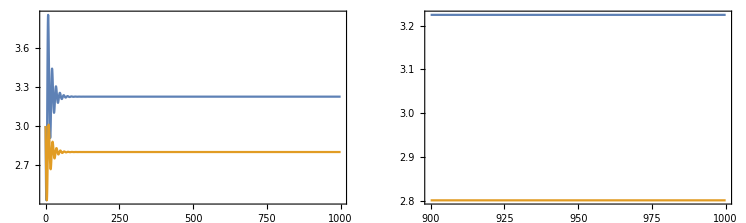

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→2.47868-3.24284 ⅈ | x[2,1][t]→3.59965-1.34044 ⅈ
x[1,1][t]→2.47868+3.24284 ⅈ | x[2,1][t]→3.59965+1.34044 ⅈ
x[1,1][t]→3.22447 | x[2,1][t]→2.80071
x[1,1][t]→10. | x[2,1][t]→0.

```mathematica
Kx=10;
a=2.2;
X0=3;Y0=3;

Tmax=1000; 
EvaluateHomogenSystem[Tmax];
solHomogen=solveHomogen[Tmax];

GraphicsGrid[{
{Plot[solHomogen,{t,0,Tmax},PlotRange->Full,Frame->True],
Plot[solHomogen,{t,Tmax*0.9,Tmax},PlotRange->Full,Frame->True]}
}]

SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify;
TableForm[SteadyStates]
```

2.4

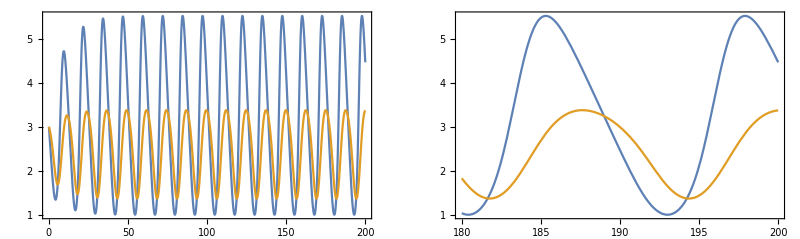

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→2.5 | x[2,1][t]→2.5
x[1,1][t]→2.91667-3.30719 ⅈ | x[2,1][t]→3.75-1.1024 ⅈ
x[1,1][t]→2.91667+3.30719 ⅈ | x[2,1][t]→3.75+1.1024 ⅈ
x[1,1][t]→10. | x[2,1][t]→0.

```mathematica
Kx=10;
a=2.4
X0=3;Y0=3;

Tmax=200;
EvaluateHomogenSystem[Tmax];
solHomogen=solveHomogen[Tmax];

GraphicsGrid[{
{Plot[solHomogen,{t,0,Tmax},PlotRange->Full,Frame->True],
Plot[solHomogen,{t,Tmax*0.9,Tmax},PlotRange->Full,Frame->True]}
}]

SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify;
TableForm[SteadyStates]
```

## Solver Test

```mathematica
PlotOptionsTimeSeries={PlotRange->Full,ImageSize->Small,MaxPlotPoints->1000};
```

### Local

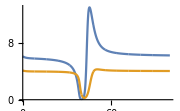

```mathematica
Kx=15;
X0=6.1;Y0=4.1;
EulerLocal[];
pltLocal=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

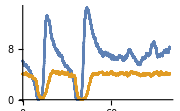

```mathematica
Kx=15;
X0=6.1;Y0=4.1;
EulerMaruyamaLocal[0.1]
pltLocalNoise=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

### Spatial

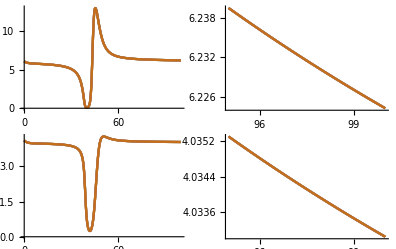

```mathematica
Kx=15;
X0=6.1;Y0=4.1;
maxsteps=10000;
Tmax=100;
EulerSpatial[Tmax,maxsteps];
pltSpatial=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

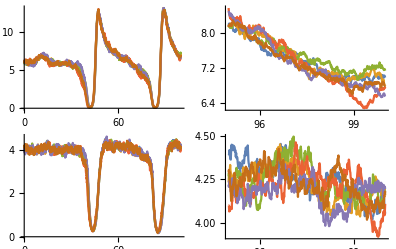

```mathematica
Kx=15;
X0=6.1;Y0=4.1;
maxsteps=10000;
Tmax=100;
EulerMaruyamaSpatial[0.1,Tmax,maxsteps];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

### Local variable Kx

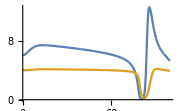

```mathematica
X0=6.1;Y0=4.1;
EulerLocalVariable[{15.5,14.5}];
pltLocal=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

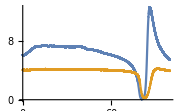

```mathematica
X0=6.1;Y0=4.1;
EulerMaruyamaLocalVariable[{15.5,14.5},0.01]
pltLocalNoise=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

### Spatial variable Kx

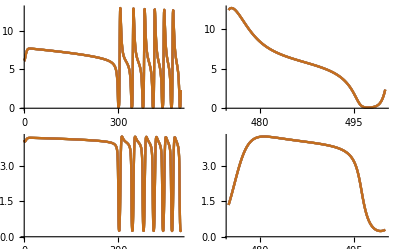

```mathematica
EulerSpatialVariable[{15.5,14.5}];
pltSpatial=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

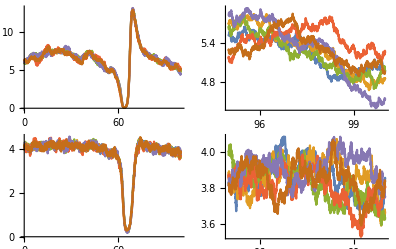

```mathematica
EulerMaruyamaSpatialVariable[{15.5,14.5},0.1];
pltSpatial=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

## Data Set Stable SN

### header

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Sorted Models/Saddle Node/export/SN"];
```

```mathematica
ExportData2S6P[name_,data_]:=Module[{},
Export[name<>".CSV",Table[Join[data[[i,1]],data[[i,2]]],{i,maxsteps}]]
];
```

```mathematica
GenFileName[]:="2_Species_6_Patches_"<>StringReplace["Kx="<>ToString[Kx]<>"_noise="<>ToString[noise],"."->"_"];
```

```mathematica
ParameterTrajectory[pars0_,pars1_,a_]:=pars0+a(pars1-pars0);
```

```mathematica
PlotOptionsTimeSeries={PlotRange->Full,ImageSize->Small,MaxPlotPoints->1000};
```

### constant pars

```mathematica
parameterList=Table[ParameterTrajectory[16,14,Kx],{Kx,0,1,0.25}]
Length[parameterList]
assf=0
```

{16.,15.5,15.,14.5,14.}

5

0

2

15.9

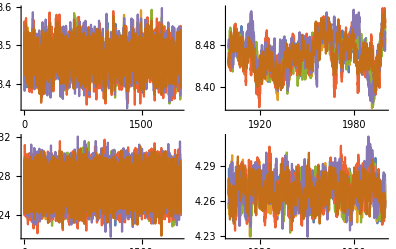

2

2_Species_6_Patches_a=3_noise=0_01

```mathematica
++assf

LoadParameters[];
Kx=parameterList[[assf]]
X0=6;Y0=4;

noise=0.01;

(* Transienten *)
Tmax0=1000;
maxsteps0=100000;
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];

initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=2000;
maxsteps=200000;
EulerMaruyamaSpatial[noise,Tmax,maxsteps,initialData];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]

assf
GenFileName[]
```

```mathematica
parameterList=Table[Kx,{Kx,15.2,14.8,-0.025}];
parameterList//Length
```

41

```mathematica
parameterList=Table[Kx,{Kx,15.2,14.8,-0.025}];
For[assf=1,assf<=Length[parameterList],++assf,
LoadParameters[];
Kx=parameterList[[assf]];
X0=6;Y0=3;

noise=0.01;

(* Transienten *)
Tmax0=1000;
maxsteps0=100000;
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];

initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=2000;
maxsteps=200000;
EulerMaruyamaSpatial[noise,Tmax,maxsteps,initialData];

ExportData2S6P[GenFileName[],data];
];
```

### variable Kx

```mathematica
GenFileName[]:="2_Species_6_Patches_"<>StringReplace["Kx="<>ToString[KxInterval[[1]]]<>"_to_"<>ToString[KxInterval[[2]]]<>"_noise="<>ToString[noise],"."->"_"];
GenFileName[tag_]:="2_Species_6_Patches_"<>StringReplace["Kx="<>ToString[KxInterval[[1]]]<>"_to_"<>ToString[KxInterval[[2]]]<>"_noise="<>ToString[noise],"."->"_"]<>"_("<>ToString[tag]<>")";
```

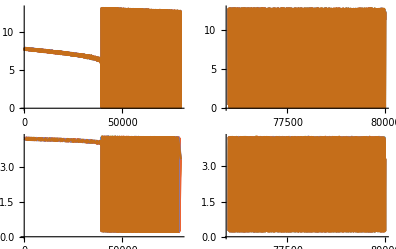

2_Species_6_Patches_Kx=15_5_to_14_5_noise=0_01

```mathematica
(* Parameter *)
LoadParameters[];
KxInterval={15.5,14.5};
noise=0.01;

(* Transienten *)
Tmax0=1000;
maxsteps0=100000;

Kx=KxInterval[[1]];
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];
initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=80000;
maxsteps=8000000;
EulerMaruyamaSpatialVariable[KxInterval,noise,Tmax,maxsteps,initialData];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
GenFileName[]
```

```mathematica
ExportData2S6P[GenFileName[],data];
```

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Time Series/Continuous changing parameters"]

(* Parameter *)
KxInterval={15.1,14.9};
noise=0.01;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;

Kx=KxInterval[[1]];

EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];
initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=4200;
maxsteps=4200000;
EulerMaruyamaSpatialVariable[KxInterval,noise,Tmax,maxsteps,initialData];

ExportData2S6P[GenFileName[],data];
```

SetDirectory::cdir: Cannot set current directory to /local.work/brechtel/Early Warning Signs/Time Series/Continuous changing parameters.

$Failed

## Data Set Stable Hopf

### header

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Sorted Models/Saddle Node/export/hopf"];
```

```mathematica
ExportData2S6P[name_,data_]:=Module[{},
Export[name<>".CSV",Table[Join[data[[i,1]],data[[i,2]]],{i,maxsteps}]]
];
```

```mathematica
GenFileName[]:="2_Species_6_Patches_"<>StringReplace["a="<>ToString[a]<>"_noise="<>ToString[noise],"."->"_"];
```

```mathematica
ParameterTrajectory[pars0_,pars1_,a_]:=pars0+a(pars1-pars0);
```

```mathematica
PlotOptionsTimeSeries={PlotRange->Full,ImageSize->Small,MaxPlotPoints->1000};
```

### constant pars

```mathematica
parameterList=Table[ParameterTrajectory[2.1,2.4,a],{a,0,1,0.25}]
Length[parameterList]
assf=0
```

{2.1,2.175,2.25,2.325,2.4}

5

0

1

2.1

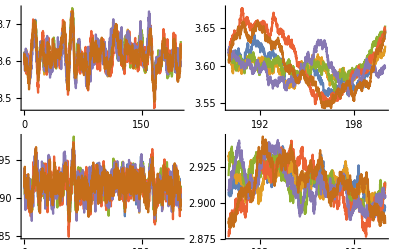

1

2_Species_6_Patches_a=2_1_noise=0_01

```mathematica
++assf

Kx=10;
a=parameterList[[assf]]
X0=3;Y0=3;

noise=0.01;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];

initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=200;
maxsteps=200000;
EulerMaruyamaSpatial[noise,Tmax,maxsteps,initialData];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]

assf
GenFileName[]
```

```mathematica
parameterList=Table[Kx,{Kx,2.1,2.4,0.01}];
parameterList//Length
```

31

```mathematica
parameterList=Table[a,{a,2.1,2.4,0.01}];
For[assf=1,assf<=Length[parameterList],++assf,
Kx=10;
a=parameterList[[assf]];
X0=3;Y0=3;

noise=0.01;

(* Transienten *)
Tmax0=1000;
maxsteps0=100000;
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];

initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=2000;
maxsteps=200000;
EulerMaruyamaSpatial[noise,Tmax,maxsteps,initialData];

ExportData2S6P[GenFileName[],data];
];
```

### variable a

```mathematica
GenFileName[]:="2_Species_6_Patches_"<>StringReplace["a="<>ToString[aInterval[[1]]]<>"_to_"<>ToString[aInterval[[2]]]<>"_noise="<>ToString[noise],"."->"_"];
GenFileName[tag_]:="2_Species_6_Patches_"<>StringReplace["a="<>ToString[aInterval[[1]]]<>"_to_"<>ToString[aInterval[[2]]]<>"_noise="<>ToString[noise],"."->"_"]<>"_("<>ToString[tag]<>")";
```

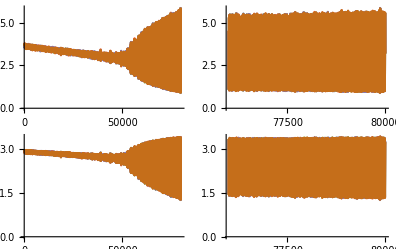

2_Species_6_Patches_a=2_1_to_2_4_noise=0_01

```mathematica
(* Parameter *)
LoadParameters[];
aInterval={2.1,2.4};
noise=0.01;

(* Transienten *)
Tmax0=1000;
maxsteps0=100000;

a=aInterval[[1]];
EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];
initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=80000;
maxsteps=8000000;
EulerMaruyamaSpatialVariableA[aInterval,noise,Tmax,maxsteps,initialData];
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
GenFileName[]
```

```mathematica
ExportData2S6P[GenFileName[],data];
```

```mathematica
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Time Series/Continuous changing parameters"]

(* Parameter *)
aInterval={2.1,2.4};
noise=0.01;

(* Transienten *)
Tmax0=100;
maxsteps0=100000;

a=aInterval[[1]];

EulerMaruyamaSpatial[noise,Tmax0,maxsteps0];
initialData=data[[maxsteps0]];

(* Daten nach Einschwingen *)
Tmax=4200;
maxsteps=4200000;
EulerMaruyamaSpatialVariable[KxInterval,noise,Tmax,maxsteps,initialData];

ExportData2S6P[GenFileName[],data];
```

SetDirectory::cdir: Cannot set current directory to /local.work/brechtel/Early Warning Signs/Time Series/Continuous changing parameters.

$Failed